```mathematica
row[m_,n_,theta_,phi_]=1+0.2*Sin[m*theta]*Sin[n*phi];
```

```mathematica
Manipulate[
SphericalPlot3D[
row[m,n,theta,phi],{theta, 0,2*π},{phi,0,2*π}
],{{m,6},1,8,1},{{n,5},1,8,1}
]
```

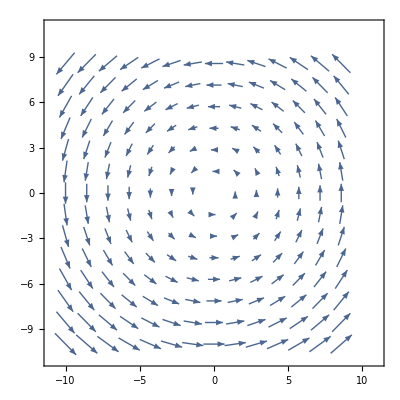

```mathematica
field[x_,y_]={-y,x};
VectorPlot[field[x,y],{x,-10,10},{y,-10,10},AxesOrigin->{0,0}]
```

```mathematica
field[x_,y_,z_]={-z,y,x};
VectorPlot3D[field[x,y,z],{x,-10,10},{y,-10,10},{z,-10,10},VectorStyle->{Arrowheads[0.02]},VectorColorFunction->"Rainbow"]
```

-Graphics3D-

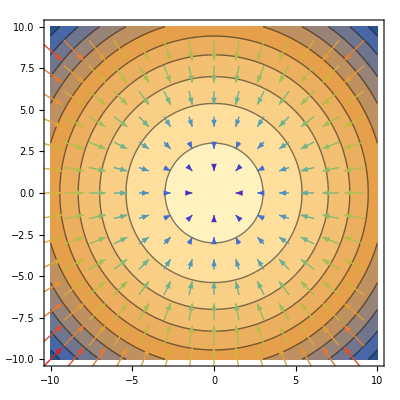

```mathematica
f[x_,y_]=9-x^2-y^2;
gradient[x_,y_]={D[f[x,y],x],D[f[x,y],y]};
gradient3D[x_,y_]={D[f[x,y],x],D[f[x,y],y],-1};
Show[
ContourPlot[f[x,y],{x,-10,10},{y,-10,10}],
VectorPlot[gradient[x,y],{x,-10,10},{y,-10,10},VectorColorFunction->"Rainbow"]
]
```

```mathematica
Show[
ContourPlot3D[z==f[x,y],{x,-3,3},{y,-3,3},{z,-10,10}],
VectorPlot3D[{gradient3D[x,y]},{x,-3,3},{y,-3,3},{z,0,10},VectorColorFunction->"Rainbow",VectorStyle->{Arrowheads[0.02]}]
]
```

-Graphics3D-